```mathematica
SetDirectory[NotebookDirectory[]]
```

/data2/users/sanderson/Research/KLStats/Isochrone/With4MOSTErrors

Conversion factor between km/s and kpc/Myr to a zillion (16) sigfigs

```mathematica
kmsTokpcMyr=0.001022729843472133;
```

Define the “true” potential

```mathematica
Phi[r_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])
PhiEff[r_,L_,M_,b_]:=-M/(b+Sqrt[b^2+r^2])+L^2/(2 r^2)
vcirc[r_,M_,b_]:=Sqrt[(M r^2)/(Sqrt[b^2+r^2] (b+Sqrt[b^2+r^2])^2)]
```

```mathematica
Jr[r_,pr_,L_,M_,b_]:=M/Sqrt[-pr^2-L^2/r^2+2 M/(b+Sqrt[b^2+r^2])]-1/2 (L+Sqrt[L^2+4 M b]/2)
```

Construct streams as clumps in (Jr, L, L_z) space

Note that we need all three numbers to describe the collection of orbits so that we know the relative inclinations - we can assume phase-mixing though so the distribution in Θ is just uniform from 0 to 2π for these things

```mathematica
Ns=1;
sigmas={0.005}(*,0.02,0.05,0.07}*)(*RandomReal[{0,.1},Ns]*)
```

{0.005}

We have to sample the angular momentum as a (magnitude, angle) pair, since L and Lz are not strictly independent of one another (you can’t have Lz>L). So this table constructs distributions that are Gaussian in cosi, L and Jr, and then we convert to Lz after the distribution is sampled.

```mathematica
spikyDist=MixtureDistribution[RandomReal[{0.1,1},Ns],Table[MultinormalDistribution[{RandomReal[{-1,1}],RandomReal[{2,10}],RandomReal[{0,10}]},DiagonalMatrix[{sigmas[[i]]/10,sigmas[[i]],sigmas[[i]]}]],{i,1,Ns}]]
```

MultinormalDistribution[{-0.70215,2.88154,8.43185},{{0.0005,0.,0.},{0.,0.005,0.},{0.,0.,0.005}}]

```mathematica
Nstars=50000;
```

```mathematica
Dimensions[trueJrL=RandomVariate[spikyDist,Nstars]]
```

{50000,3}

Throw out anything outside the cos i range [-1,1] or with negative Jr and resample:

```mathematica
For[i=1,i≤Nstars,i++, While[(Abs[trueJrL[[i,1]]]>1)||(trueJrL[[i,3]]<0),trueJrL[[i]]=RandomVariate[spikyDist]]]
```

```mathematica
Select[trueJrL[[All,1]],#<-1&]
```

{}

```mathematica
Select[trueJrL[[All,3]],#<0&]
```

{}

```mathematica
Dimensions[trueActions=Transpose[{trueJrL[[All,1]]*trueJrL[[All,2]],trueJrL[[All,2]],trueJrL[[All,3]]}]]
```

{50000,3}

The random realization shows us that the points fall in clumps in action space:

```mathematica
ListPointPlot3D[trueActions,PlotRange->{{-12,12},{-12,12},{0,12}},AspectRatio->1]
```

-Graphics3D-

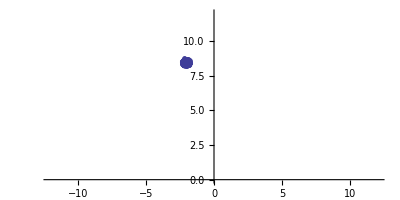

```mathematica
ListPlot[trueActions[[All,{1,3}]],PlotRange->{{-12,12},{0,12}},AspectRatio->1/2]
```

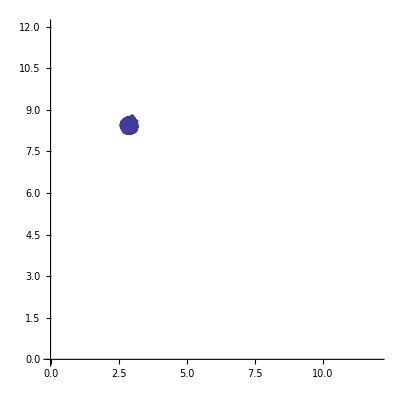

```mathematica
ListPlot[trueActions[[All,{2,3}]],PlotRange->{{0,12},{0,12}},AspectRatio->1]
```

We also need the angles, which are phase-mixed:

```mathematica
Dimensions[trueAngles=Transpose[{RandomReal[{0,2π},Nstars],RandomReal[{0,2π},Nstars],RandomReal[{0,2π},Nstars]}]]
```

{50000,3}

```mathematica
Dimensions[initAngles=Transpose[{RandomVariate[NormalDistribution[1.0,2π/1000],Nstars],RandomVariate[NormalDistribution[2.0,2π/1000],Nstars],RandomVariate[NormalDistribution[6.0,2π/1000],Nstars]}]]
```

{50000,3}

```mathematica
(*initAngles=Table[{0,0,0},{i,1,Nstars}];*)
```

Convert coordinates to configuration space (x,v)

This is done using a C program called through MathLink

```mathematica
link=Install["../AAToCart/aa_to_cart_math"]
```

LinkObject[/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math,9,8]

```mathematica
trueCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,trueCart[[i]]=AAToCart[trueActions[[i]],trueAngles[[i]]]]
```

```mathematica
initCart=Table[{0,0,0,0,0,0},{i,1,Nstars}];
```

```mathematica
For[i=1, i≤Nstars, i++,initCart[[i]]=AAToCart[trueActions[[i]],initAngles[[i]]]]
```

```mathematica
Uninstall[link]
```

/data2/users/sanderson/Research/KLStats/Isochrone/AAToCart/aa_to_cart_math

### plots of the cartesian distribution

```mathematica
ListPointPlot3D[trueCart[[All,1;;3]],PlotRange->{{-80,80},{-80,80},{-80,80}},AspectRatio->1]
```

-Graphics3D-

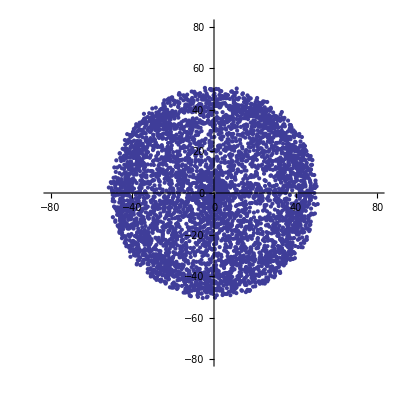

```mathematica
ListPlot[trueCart[[All,1;;2]],PlotRange->{{-80,80},{-80,80}},AspectRatio->1]
```

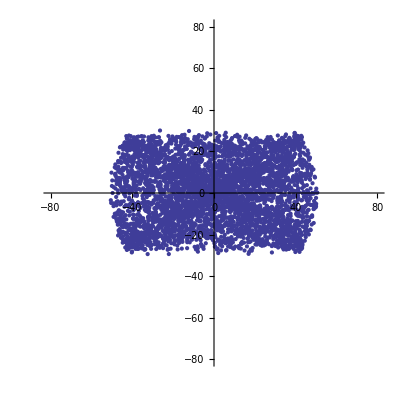

```mathematica
ListPlot[trueCart[[All,2;;3]],PlotRange->{{-80,80},{-80,80}},AspectRatio->1]
```

```mathematica
ListPointPlot3D[initCart[[All,1;;3]],PlotRange->All(*PlotRange->{{-50,50},{-50,50},{-5,5}},AspectRatio->1*)]
```

-Graphics3D-

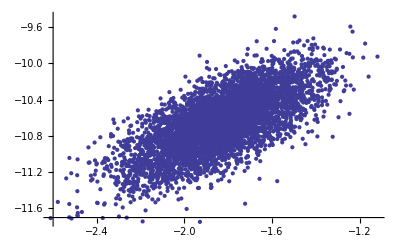

```mathematica
ListPlot[initCart[[All,1;;2]],PlotRange->All(*{{-60,40},{-50,50}},AspectRatio->1*)]
```

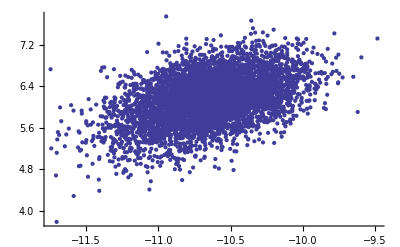

```mathematica
ListPlot[initCart[[All,2;;3]],PlotRange->All(*{{-60,-40},{15,35}},AspectRatio->1*)]
```

```mathematica
{x0,y0,z0,vx0,vy0,vz0}=Mean[initCart]
```

{-1.83263,-10.6497,6.14976,0.0542006,-0.725726,0.359278}

```mathematica
{dx,dy,dz,dvx,dvy,dvz}={initCart[[All,1]]-x0,initCart[[All,2]]-y0,initCart[[All,3]]-z0,initCart[[All,4]]-vx0,initCart[[All,5]]-vy0,initCart[[All,6]]-vz0};
```

```mathematica
Mean[Sqrt[dx^2+dy^2+dz^2]]
```

0.531404

```mathematica
Mean[Sqrt[dvx^2+dvy^2+dvz^2]]*978
```

26.1383

```mathematica
Sqrt[(x0+8.0)^2+y0^2+z0^2]
```

13.7576

```mathematica
ListPointPlot3D[978*trueCart[[All,4;;6]],PlotRange->{{-1000,1000},{-1000,1000},{-1000,1000}},AspectRatio->1]
```

-Graphics3D-

```mathematica
Position[trueCart[[All,1]],Indeterminate]
```

{}

### Split up coordinates into positions and velocities

```mathematica
initPositions=initCart[[All,1;;3]];
initVelocities=initCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
truePositions=trueCart[[All,1;;3]];
trueVelocities=trueCart[[All,4;;6]]/kmsTokpcMyr;
```

```mathematica
trueDists=Sqrt[(truePositions[[All,1]]-8)^2+truePositions[[All,2]]^2+truePositions[[All,3]]^2];
```

### Histogram of distances from the Sun to the stream stars

```mathematica
dbins=Table[id,{id,0,80,1}];
dcounts=BinCounts[trueDists,{dbins}];
```

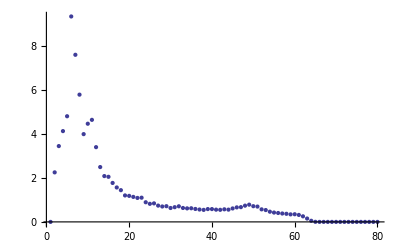

```mathematica
ListPlot[Transpose[{dbins[[2;;Length[dbins]]],dcounts/(dbins[[2;;Length[dbins]]]^2)}],PlotRange->All]
```

Convert (x,v) to observables, convolve with errors, and convert back to (x’,v’)

NOTE: make sure that these four filenames are the same in here and in data_realization_gaia.f!!!!

```mathematica
fnamePosIn="pos.test.dat"
fnamePosOut="newpos.test.dat"
fnameVelIn="vel.test.dat"
fnameVelOut="newvel.test.dat"
fnameObsOut="obs.dat"
```

pos.test.dat

newpos.test.dat

vel.test.dat

newvel.test.dat

obs.dat

```mathematica
pStream=OpenWrite[fnamePosIn,BinaryFormat->False]
vStream=OpenWrite[fnameVelIn,BinaryFormat->False]
```

OutputStream[pos.test.dat,94]

OutputStream[vel.test.dat,95]

```mathematica
Write[pStream,Length[truePositions]];
Export[pStream,truePositions,"Data"];
Export[vStream,trueVelocities,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.test.dat

vel.test.dat

## At this point, manually run data_realizations_4MOST

```mathematica
pStream=OpenRead[fnamePosOut];
vStream=OpenRead[fnameVelOut];
oStream=OpenRead[fnameObsOut];
n1=Read[pStream,Number]
n2=Read[oStream,Number]
Dimensions[convPositions=ReadList[pStream,{Number,Number,Number}]]
Dimensions[convVelocities=ReadList[vStream,{Number,Number,Number}]]
Dimensions[convObs=ReadList[oStream,{Number,Number,Number,Number,Number,Number,Number,Number,Number,Number,Number}]]
Close[pStream];
Close[vStream];
Close[oStream];
```

50000

50000

{50000,3}

{50000,3}

{50000,11}

columns of observational file are vmag, alpha, delta, parallax, par error, mu_alpha, pm error, mu_delta, pm error, RV, RV error

Data quality cuts (on observational data)

### Histogram of magnitudes - cut out V>20

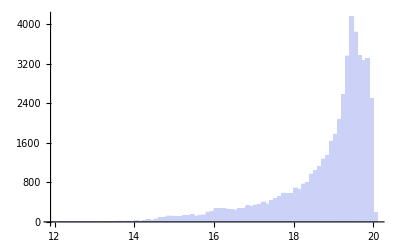

```mathematica
Histogram[convObs[[All,1]]]
```

```mathematica
Tally[magSel=Thread[convObs[[All,1]]<20]]
```

{{True,49810},{False,190}}

### Cut out negative parallaxes, and those with huge errors

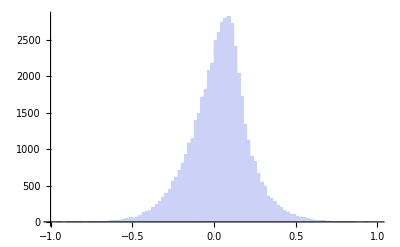

```mathematica
Histogram[convObs[[All,4]],{-1,1,.02}]
```

```mathematica
Tally[posParSel=Thread[(convObs[[All,4]]>0)]]
```

{{True,30612},{False,19388}}

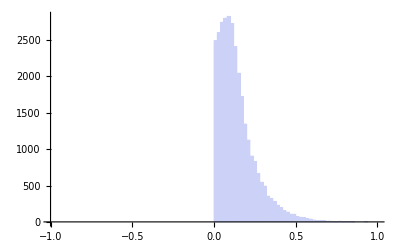

```mathematica
Histogram[Pick[convObs[[All,4]],posParSel],{-1,1,.02}]
```

```mathematica
Tally[hugeParErrSel=Thread[Abs[convObs[[All,5]]]< 1000]]
```

{{True,49810},{False,190}}

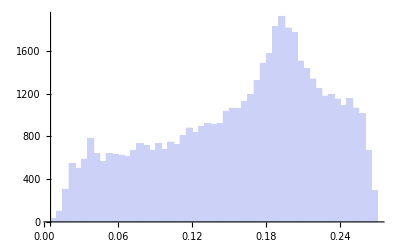

```mathematica
Histogram[Pick[convObs[[All,5]],hugeParErrSel],PlotRange->All]
```

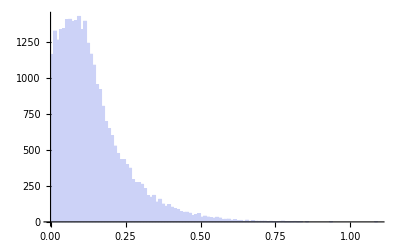

```mathematica
Histogram[Pick[convObs[[All,4]],Thread[posParSel&&hugeParErrSel]],PlotRange->All]
```

### Dataquality cut on parallaxes

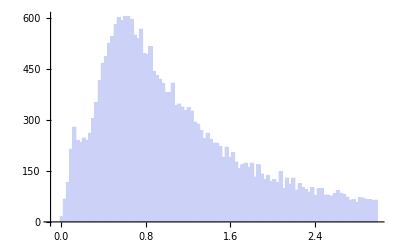

```mathematica
Histogram[Pick[convObs[[All,5]]/convObs[[All,4]],Thread[posParSel&&hugeParErrSel]],{-.1,3,.03}]
```

```mathematica
Tally[dqParSel=Thread[Abs[convObs[[All,5]]/convObs[[All,4]]]<0.3]]
```

{{False,47992},{True,2008}}

### Dataquality cut on proper motions is basically the same as for parallaxes - errors are proportional

### Dataquality cut on RVs

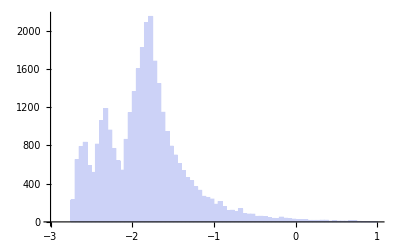

```mathematica
Histogram[Log10[convObs[[All,11]]/convObs[[All,10]]],{-3,1,.05}]
```

```mathematica
Tally[dqRVSel=Thread[Abs[convObs[[All,11]]/convObs[[All,10]]]<0.3]]
```

{{True,48557},{False,1443}}

### Combining all the cuts together

```mathematica
Tally[allSels=Thread[magSel&&posParSel&&hugeParErrSel&&dqParSel&&dqRVSel]]
```

{{False,45050},{True,4950}}

```mathematica
Dimensions[tpSel=Pick[truePositions,allSels]]
```

Dimensions::argt: Dimensions called with 0 arguments; 1 or 2 arguments are expected.

Dimensions[]

```mathematica
Dimensions[cpSel=Pick[convPositions,allSels]]
```

{4950,3}

```mathematica
Dimensions[tvSel=Pick[trueVelocities,allSels]]
```

{1959,3}

```mathematica
Dimensions[cvSel=Pick[convVelocities,allSels]]
```

{4950,3}

### Plots examining error behavior etc

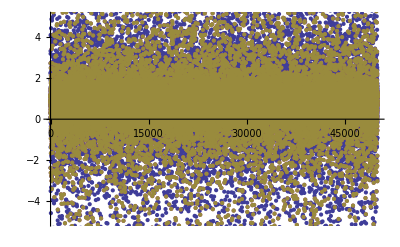

```mathematica
ListPlot[Transpose[(truePositions-convPositions)/truePositions],PlotRange->{-5,5}]
```

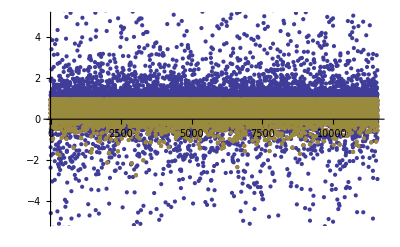

```mathematica
ListPlot[Transpose[(tpSel-cpSel)/tpSel],PlotRange->{-5,5}]
```

```mathematica
convDists=Sqrt[(convPositions[[All,1]]-8)^2+convPositions[[All,2]]^2+convPositions[[All,3]]^2];
```

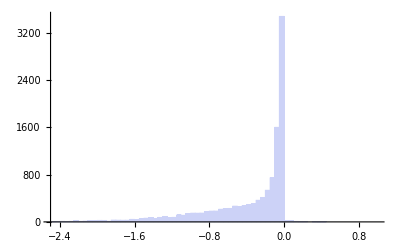

```mathematica
Histogram[Pick[Log10[Abs[(trueDists-convDists)]/trueDists],allSels],{-2.5,1,0.05}]
```

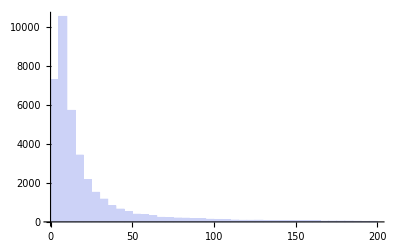

```mathematica
Histogram[Pick[convDists,Thread[!allSels]],{0,200,5}]
```

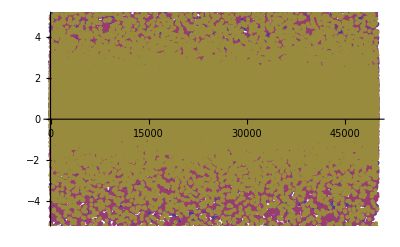

```mathematica
ListPlot[Transpose[(trueVelocities-convVelocities)/trueVelocities],PlotRange->{-5,5}]
```

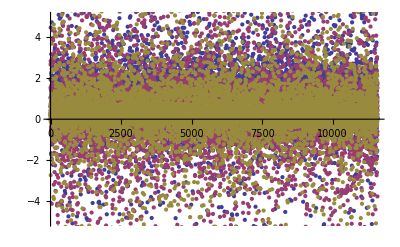

```mathematica
ListPlot[Transpose[(tvSel-cvSel)/tvSel],PlotRange->{-5,5}]
```

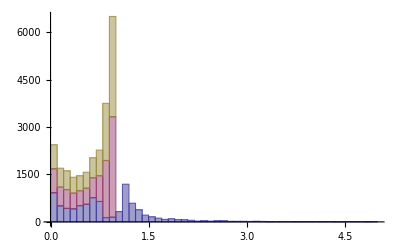

```mathematica
Histogram[Transpose[(tpSel-cpSel)/tpSel],{0,5,.1},ChartLayout->"Stacked"]
```

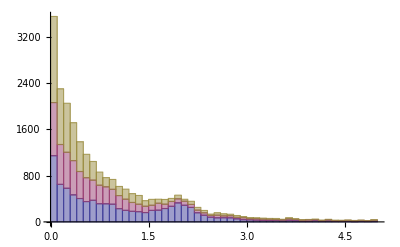

```mathematica
Histogram[Transpose[(tvSel-cvSel)/tvSel],{0,5,.1},ChartLayout->"Stacked"]
```

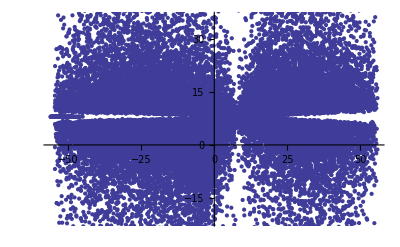

```mathematica
ListPlot[Transpose[{truePositions[[All,1]],convPositions[[All,1]]}]]
```

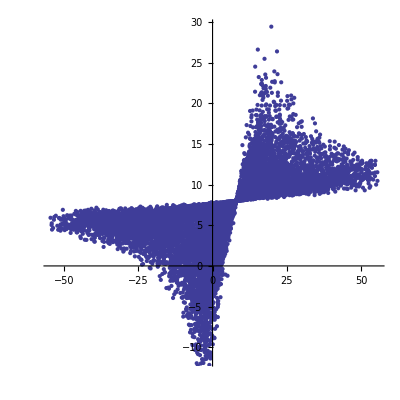

```mathematica
ListPlot[Transpose[{tpSel[[All,1]],cpSel[[All,1]]}],AspectRatio->1]
```

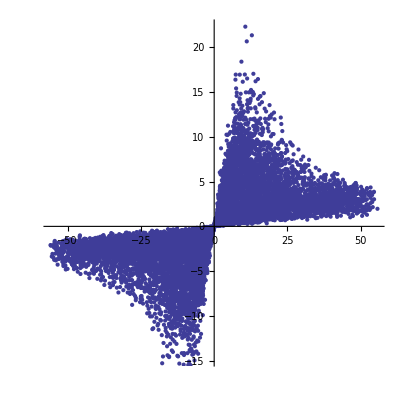

```mathematica
ListPlot[Transpose[{tpSel[[All,2]],cpSel[[All,2]]}],AspectRatio->1]
```

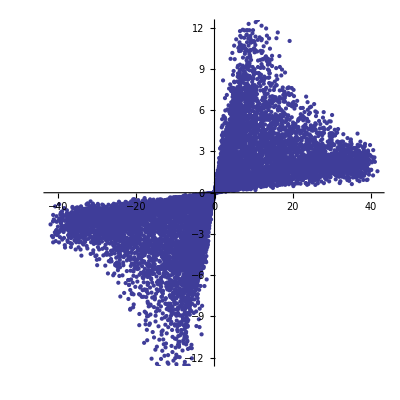

```mathematica
ListPlot[Transpose[{tpSel[[All,3]],cpSel[[All,3]]}],AspectRatio->1]
```

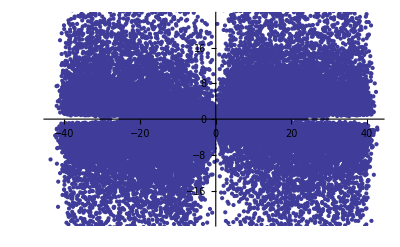

```mathematica
ListPlot[Transpose[{truePositions[[All,3]],convPositions[[All,3]]}]]
```

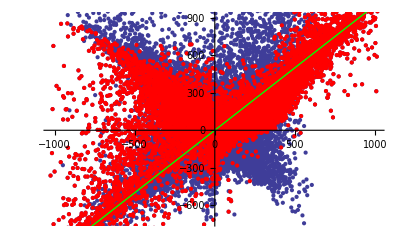

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,1]],convVelocities[[All,1]]}]],ListPlot[Transpose[{tvSel[[All,1]],cvSel[[All,1]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

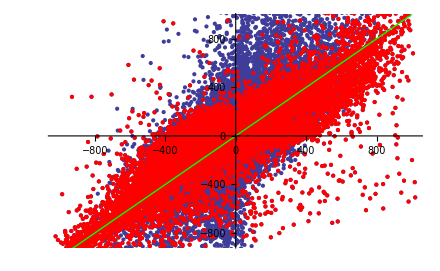

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,2]],convVelocities[[All,2]]}]],ListPlot[Transpose[{tvSel[[All,2]],cvSel[[All,2]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

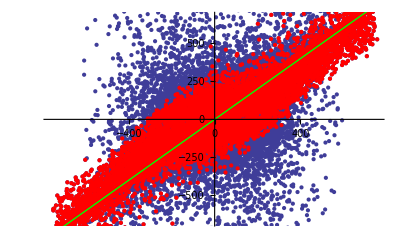

```mathematica
Show[ListPlot[Transpose[{trueVelocities[[All,3]],convVelocities[[All,3]]}]],ListPlot[Transpose[{tvSel[[All,3]],cvSel[[All,3]]}],PlotStyle->Red],Epilog->{Green,Thick,Line[{{-1000,-1000},{1000,1000}}]}]
```

Convert (x’,v’) to (Jr’,L’,Lz’)

```mathematica
fnameCleanPosIn="pos.clean.dat"
fnameCleanVelIn="vel.clean.dat"
```

pos.clean.dat

vel.clean.dat

```mathematica
pStream=OpenWrite[fnameCleanPosIn,BinaryFormat->False]
vStream=OpenWrite[fnameCleanVelIn,BinaryFormat->False]
```

OutputStream[pos.clean.dat,72]

OutputStream[vel.clean.dat,73]

```mathematica
Write[pStream,Length[cpSel]];
Export[pStream,cpSel,"Data"];
Export[vStream,cvSel,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

pos.clean.dat

vel.clean.dat

## At this point manually run cartToAA

```mathematica
Dimensions[convJ=ReadList["newJ.test.dat",{Number,Number,Number}]]
```

{4950,3}

Some stuff has unbound orbits, so select those out

```mathematica
Tally[boundSel=Thread[convJ[[All,3]]!=0]]
```

{{True,4664},{False,286}}

```mathematica
Dimensions[convJbound=Pick[convJ,boundSel]]
```

{4664,3}

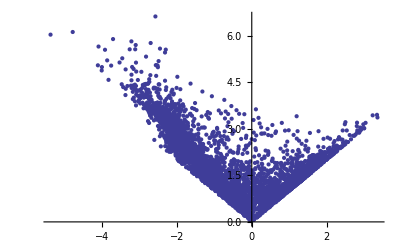

```mathematica
ListPlot[convJbound[[All,{1,2}]]]
```

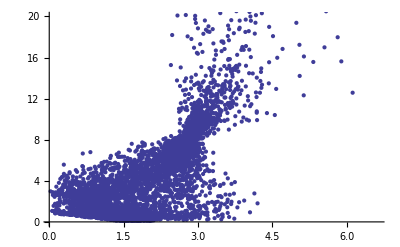

```mathematica
ListPlot[convJbound[[All,{2,3}]],PlotRange->{0,20}]
```

```mathematica
ListPointPlot3D[convJbound]
```

-Graphics3D-

```mathematica
Dimensions[tJSel=Pick[Pick[trueActions,allSels],boundSel]]
```

Pick::argtu: Pick called with 1 argument; 2 or 3 arguments are expected.

{1}

```mathematica
ListPlot[Transpose[{tJSel[[All,3]],convJbound[[All,3]]}],PlotRange->{{0,20},{0,20}},AspectRatio->1]
```

Pick::argtu: Pick called with 1 argument; 2 or 3 arguments are expected.

Transpose::nmtx: The first two levels of the one-dimensional list {Pick[True], {3.34814, 0.48759, 7.48781, 0.511859, 4.51279, 22.6112, 7.49893, 5.40106, 7.05854, 10.5659, 0.622595, 7.82748, 6.84951, 19.6946, 8.00643, 0.6729, 6.57852, 3.34293, « 15 », 8.31856, 2.80453, 4.11606, 8.35976, 1.89459, 7.69482, 0.207501, 4.74439, 7.22327, 8.0756, 0.148958, 0.819532, 10.6257, 7.153, 7.63477, 4.8307, 9.22632, « 4614 »}} cannot be transposed.

ListPlot::lpn: Transpose[{Pick[True], {3.34814, 0.48759, 7.48781, 0.511859, 4.51279, 22.6112, 7.49893, 5.40106, 7.05854, 10.5659, 0.622595, 7.82748, 6.84951, 19.6946, 8.00643, 0.6729, 6.57852, « 17 », 2.80453, 4.11606, 8.35976, 1.89459, 7.69482, 0.207501, 4.74439, 7.22327, 8.0756, 0.148958, 0.819532, 10.6257, 7.153, 7.63477, 4.8307, 9.22632, « 4614 »}}] is not a list of numbers or pairs of numbers.

ListPlot[Transpose[{Pick[True],{3.34814,0.48759,7.48781,0.511859,4.51279,22.6112,7.49893,5.40106,7.05854,10.5659,0.622595,7.82748,6.84951,19.6946,8.00643,0.6729,6.57852,3.34293,0.177718,0.402998,0.565529,0.23949,3.26531,9.47103,7.30479,0.32464,0.638115,3.84094,5.43311,2.43587,6.2202,8.66283,0.309189,8.31856,2.80453,4.11606,8.35976,1.89459,7.69482,0.207501,4.74439,7.22327,8.0756,0.148958,0.819532,10.6257,7.153,7.63477,4.8307,9.22632,1.76745,4.34456,4.31607,4.05771,5.72707,0.527913,0.281366,1.15745,4.92422,0.822012,0.738191,0.323291,8.60563,1.49646,3.59417,1.09922,1.28691,11.283,8.54357,10.9337,2.75598,0.589037,1.82666,18.7548,17.5707,4.06897,18.3294,7.10315,4.79029,3.46364,7.18184,7.53476,7.55284,2.81997,8.7527,0.289375,1.90606,0.369938,2.57364,0.265516,2.71431,12.0199,8.28267,0.123412,10.0081,0.575596,0.28389,5.13008,3.02124,3.8774,0.155033,0.870373,6.89071,9.49387,7.01777,1.96432,3.18103,0.418769,1.42481,3.97358,0.604918,3.14438,0.380538,0.597224,11.6678,0.488637,6.45373,8.78842,1.94417,7.99454,0.548936,3.70544,0.719808,0.559186,6.27933,1.93265,0.789879,0.241807,2.65526,0.384911,0.633873,1.53569,19.7524,5.09999,0.939979,2.49688,2.67529,0.36111,4.58537,5.66554,3.82425,26.0776,2.75548,4.77047,1.49808,0.695286,0.182923,7.8356,3.20901,2.40715,1.47837,2.48099,6.40429,22.6131,8.92014,1.10369,3.07116,8.4398,0.5948,2.02575,6.80322,0.516119,0.35701,0.589901,4.92086,8.20956,6.01681,8.59758,2.45792,0.645709,3.72386,0.647667,6.82919,0.993855,0.543676,11.7377,3.75993,6.93178,0.67082,0.780191,11.4587,0.17174,142.241,0.534878,3.4887,3.76623,0.584939,4.7063,6.33453,0.288909,14.8988,8.34566,12.9243,7.74629,5.14564,5.21164,8.54262,10.7839,0.440076,20.4421,3.64136,8.01221,4.31016,1.16762,4.7033,8.23421,2.34566,7.71622,0.514318,5.38463,0.70607,1.76867,0.569917,5.88829,6.96708,2.62881,0.693653,2.99492,0.804546,7.77693,7.8586,3.57866,7.96647,6.18349,1.27332,0.623099,7.13793,2.23044,1.37123,1.69149,1.02665,1.01453,54.7869,13.5046,0.551658,5.50473,8.47016,6.44501,0.284953,3.86495,0.702241,3.12285,1.87921,36.8089,0.963105,6.82183,9.82278,4.85207,4.57469,0.452267,5.09351,0.15048,2.38858,0.185202,2.37071,1.8303,1.69478,7.73303,5.492,7.0909,3.54634,0.77718,6.27354,3.11124,2.45037,0.326957,21.325,0.784657,2.64586,8.65169,0.454254,8.93998,0.667038,0.124711,7.78966,1.13113,4.20109,8.92188,7.55561,0.947003,0.214848,6.38323,0.527417,0.246537,7.64634,5.78697,6.05681,3.16445,0.238805,2.01985,7.03902,4.70464,8.56895,3.08084,2.47763,0.988186,6.35944,2.54951,4.87346,3.86477,4.03017,2.90693,13.22,10.5881,0.631411,0.384077,3.62219,4.59496,0.628064,1.81458,2.97543,0.41363,1.06045,11.673,0.641263,4.28829,2.02217,0.52304,0.599098,9.9577,3.12265,10.3952,0.363406,2.40435,0.974064,2.3687,3.75084,3.94154,1.1587,10.3625,0.594903,3.88217,2.01281,9.7849,7.57742,2.19647,6.9875,2.68512,0.921896,0.501539,0.305403,0.124203,8.17166,7.6797,0.142647,0.199572,2.97277,4.0645,6.73694,7.47158,5.39453,10.9813,0.651172,5.07649,6.43148,7.54419,9.20639,0.817839,2.95668,4.38438,9.85504,7.7851,11.1292,0.738504,1.73699,1.96273,5.6089,4.90979,5.29177,7.05511,7.7369,3.80711,10.9324,0.508618,7.64564,5.99039,1.58262,9.62534,1.3226,0.328657,5.20996,6.17366,7.27393,0.694172,9.70602,0.645431,0.580231,5.26279,27.5022,8.17654,2.24829,6.57908,15.2693,5.21534,0.446083,0.645378,5.93118,0.771174,23.9738,0.508218,3.22442,1.28941,5.211,1.32323,2.9969,0.951724,5.57499,4.69095,2.23767,9.92388,6.32928,0.782718,0.41437,7.95665,1.67671,2.94259,5.71896,0.70155,9.63443,6.72489,6.06577,4.50456,1.32237,7.35713,10.0474,5.60113,9.20493,3.8098,2.36007,13.1772,0.315997,0.597347,3.64763,10.6078,4.92026,5.30761,0.393587,0.666771,8.35519,1.29206,4.56143,0.85837,9.30776,2.82581,9.14466,6.34946,0.811496,1.41608,8.48702,0.267889,0.910237,0.501088,8.26612,0.575763,0.717504,2.50966,0.311344,0.803452,0.430243,1.44137,0.460967,6.28535,0.534089,0.600732,0.623474,7.94306,8.61051,2.37414,9.12977,0.242882,3.00982,2.53457,0.158558,8.55549,1.85741,14.9141,11.3113,9.76536,0.423928,0.494243,0.814185,7.29317,9.34174,3.6077,5.55536,7.95162,0.865742,4.44861,3.85284,4.55162,2.67625,4.7811,12.5267,1.14208,3.28693,8.62827,8.72869,6.34992,7.51862,0.200348,7.25225,0.853956,7.46078,55.9727,0.431576,2.01874,0.490988,0.566977,0.571617,18.55,2.40957,7.76984,10.0015,4.08091,0.621535,5.5541,0.683343,7.11299,24.378,3.5008,2.01932,8.75576,12.2152,10.8165,0.413091,5.84517,6.4261,0.442648,7.75305,1.86348,6.14558,4.91036,8.27034,4.94688,7.71426,1.91082,7.44933,2.85348,5.80647,0.559371,0.565893,2.06479,6.82,1.2821,3.63232,14.647,10.7501,0.30821,0.354752,2.61941,5.55252,6.09258,9.016,0.9989,8.43415,3.59598,3.16295,1.22186,0.873577,8.75448,7.95846,3.61701,6.11582,52.4478,0.754729,14.9028,2.42138,5.06355,0.540611,4.62424,2.15519,2.51467,7.81768,4.14352,8.26864,20.5022,6.37328,4.72878,0.808629,10.2576,0.251902,10.4599,6.20403,0.447562,0.414276,6.89601,7.9122,2.87933,0.291062,9.4573,5.97337,0.757378,0.213632,0.660227,5.29551,8.28646,8.97952,0.506436,0.777082,2.52257,3.69466,10.624,0.151774,7.41302,0.941622,4.44279,9.34311,5.59143,0.284184,3.80321,0.790229,3.03674,1.66168,6.95261,7.31207,2.62437,1.08473,2.51696,5.68295,0.167703,1.71219,0.354075,3.80273,0.358571,1.81234,4.28369,0.959311,8.35789,0.262529,6.15971,1.95145,19.3811,15.9784,7.6013,0.984535,2.1862,7.34069,3.8732,2.59939,7.43254,8.1771,5.6648,9.51711,8.98097,0.486025,4.2092,3.03244,3.63643,2.71755,11.3369,0.50965,4.25192,0.409047,5.80136,4.21887,0.339236,0.603088,0.484888,2.81757,0.982541,6.92373,3.50658,1.01265,3.05213,2.25601,3.83305,0.823929,5.46212,10.5932,0.478208,8.82539,2.64286,0.504284,3.1031,6.31399,8.05091,0.224223,0.606328,0.568987,0.325883,0.824219,3.70586,4.68726,0.475625,3.7221,0.198121,0.41875,0.474604,18.3102,8.33984,0.585004,6.05078,0.523065,0.592836,44.6975,106.334,1.38029,12.4509,48.4477,8.63167,3.07681,0.177302,0.699726,23.171,19.5935,5.78302,2.59197,1.02312,2.39995,0.242422,7.33789,0.120554,0.570378,0.484864,1.10276,6.75595,3.61449,17.4298,8.20875,4.73803,5.46756,0.571495,0.201703,1.89868,0.140863,9.21616,1.55109,0.980451,0.137535,0.561993,0.789834,1.29383,4.34493,3.49025,1.06219,1.42391,13.0369,0.425672,1.03593,3.70163,1.9003,12.3203,1.18821,7.79881,9.68238,3.44178,6.97892,91.1306,1.15383,3.69823,12.8243,0.164743,0.1777,0.54128,9.69687,1.55018,0.986046,0.830271,11.2176,7.19291,0.618353,5.04004,7.20874,6.10972,5.06755,1.73548,9.77045,9.23137,10.0031,5.67757,12.5769,10.9308,11.6242,3.44653,10.3053,5.63238,7.31873,6.15593,4.44582,9.01171,10.7459,0.92249,7.79635,1.22903,8.12532,0.759643,0.616477,0.186193,6.72019,3.81116,0.558687,4.13899,8.30532,6.3832,5.20058,0.546099,0.93589,3.54564,0.624498,5.04585,0.445033,0.71997,3.17779,0.752955,11.0551,0.47851,0.65094,8.22676,7.20919,3.71084,6.03909,2.14054,4.148,3.09916,8.43971,0.497307,9.60591,5.62583,8.75116,5.47604,7.21217,1.65286,2.36007,1.89058,0.629606,0.299142,67.6622,6.79748,3.86808,4.14539,0.61681,3.93547,9.49011,9.86573,9.78827,0.70236,8.18501,7.69378,6.93648,12.0531,2.5591,2.71971,1.26692,5.76468,0.413011,7.60198,6.88834,3.60275,2.62177,5.14466,15.5436,1.83242,8.41328,3.25171,4.00441,2.05798,3.0393,6.59752,1.07261,0.9973,6.29409,0.571071,4.83236,0.497532,10.098,0.540117,4.90724,0.274916,6.1919,4.41756,5.77456,4.83984,0.718334,5.4117,0.789433,0.732381,1.24452,7.6331,21.445,1.52952,8.4454,0.858259,9.86442,2.05283,7.37978,0.389198,5.11906,3.7836,9.99649,4.66423,5.7446,30.0524,6.78078,3.00998,44.2544,1.03819,5.18168,8.19483,1.26401,0.94862,0.3096,0.630951,3.31615,3.75104,4.12874,5.70622,8.50147,3.3788,2.71236,19.9967,0.785591,5.00865,1.03174,2.79035,1.18891,8.53936,7.11409,6.37613,0.217373,2.42163,2.31897,2.83808,6.35302,5.24441,5.87444,3.35078,0.750624,0.387758,0.459202,2.87594,6.3016,6.9265,6.62312,10.4099,0.266625,2.42086,0.471248,1.68482,0.165986,2.31051,3.08124,9.08626,14.7416,0.480916,0.530876,12.0922,0.921817,0.53679,5.53645,0.196675,4.41194,7.8511,12.1498,5.03186,1.99764,4.05365,4.42431,0.157664,4.85769,5.24893,3.43892,7.61886,21.0271,2.66949,0.698304,5.91073,5.93101,1.92293,11.585,5.51578,30.5859,7.52525,0.646731,3.71615,8.78878,0.700577,0.822249,0.72658,9.73721,2.76682,0.545587,8.35049,8.77404,18.5006,0.46425,11.1617,2.62276,0.65444,10.0382,8.69712,32.8312,5.39391,6.97169,0.624285,1.27928,3.01889,0.445935,1.02065,2.71066,3.34516,4.64413,28.9526,7.3051,2.30989,0.813764,7.1657,3.63644,3.4237,0.302011,0.320367,0.556286,7.7822,7.25724,10.0699,3.2343,0.708603,0.236539,2.71166,2.78409,0.463495,1.38865,20.3253,6.66897,8.11926,18.9863,3.74426,8.56527,5.13534,9.44404,3.73659,6.04675,7.94554,0.502324,9.53991,7.65727,2.95735,12.7835,5.48384,0.111329,0.334738,23.702,5.96153,0.515508,7.10719,0.447467,12.238,5.09124,2.4218,24.3254,0.599003,3.01372,1.60005,3.25209,0.165803,2.19234,1.54822,5.71927,3.63294,3.47775,11.1992,0.937207,12.8049,4.94329,45.9791,0.616431,2.95807,0.417834,1.88854,0.635432,8.84093,0.460859,2.46481,0.848813,10.6218,0.831375,16.6869,7.19179,11.7522,0.504514,0.211167,0.846921,4.48903,2.36904,8.27529,3.69894,1.30245,1.57799,0.933311,0.372538,11.441,8.6971,4.62243,4.0972,8.41021,0.488097,3.57973,0.443499,3.93439,6.79097,1.29035,3.83537,2.42525,6.73542,7.05321,1.89711,0.81196,11.8876,0.222265,5.3573,2.70241,0.540121,8.46934,2.35303,1.33759,3.60963,26.9694,0.308557,0.527975,6.93658,0.337034,4.50123,5.19428,8.32551,10.4483,0.39585,0.271352,1.89688,3.14524,7.83157,8.85062,4.70967,17.8081,0.375164,13.7708,5.41269,7.07428,0.529883,7.94447,0.283965,0.564174,3.09093,0.853325,9.50226,9.47109,0.494484,25.6669,9.40111,6.52962,8.27906,6.56272,2.23372,3.18897,0.597004,2.75225,0.319308,0.616674,7.32913,3.05126,2.16586,0.448017,8.42308,1.67322,0.781249,0.579254,0.161867,0.499399,0.58012,0.537507,0.454592,8.17103,1.97631,3.2491,5.17572,0.911861,0.653467,0.514753,4.3752,4.12518,0.357683,0.639488,7.06973,3.14378,8.56163,2.69466,5.08503,6.84307,6.06433,5.49079,10.9597,3.30757,0.644827,6.985,0.502678,3.74299,8.36708,1.55402,1.16375,1.72515,7.38726,1.79746,1.16261,3.37295,0.162791,0.979586,29.1854,1.60975,0.738855,6.90868,0.655379,0.46916,0.712883,9.27288,0.27621,0.82037,7.80361,2.07778,3.02013,5.9554,2.3014,5.86481,2.69469,0.763247,0.764351,2.53637,0.45295,6.58456,3.77727,1.96516,4.08841,6.54519,0.699982,6.34569,8.67909,3.968,2.21499,0.706937,6.81718,3.75102,1.29065,0.741122,0.503899,8.68663,4.22238,1.01403,1.91546,0.265531,0.514197,1.44236,1.96669,8.51703,1.81272,13.1907,0.453612,0.480679,2.7365,4.34888,2.55409,3.25958,1.71569,2.7719,7.40132,0.330763,4.98191,7.81515,2.84154,4.94165,2.02794,6.06097,8.55575,2.64855,1.26701,0.664539,5.05702,24.0451,9.93491,4.65314,10.4181,11.2443,4.81075,0.265555,2.63784,8.45284,0.345711,0.212255,0.851827,2.09138,12.8816,9.77027,0.154185,3.63055,7.99788,0.54191,7.43079,9.182,4.1173,40.7463,8.63299,1.42289,1.78159,10.6287,7.26865,6.51091,1.29115,0.199515,11.4239,28.845,0.872219,5.8742,13.4875,0.680088,0.598034,6.81475,6.52979,1.68456,3.6841,2.86272,5.04722,0.57302,2.60893,1.00511,5.48722,0.351317,0.504693,0.391666,0.4279,5.1281,8.32519,1.21615,0.618096,0.946494,0.682678,6.27229,0.471262,32.8299,0.585386,0.38339,3.01748,13.146,6.86174,1.22613,14.4758,11.036,7.02048,2.86113,6.73643,0.846597,0.745368,1.15836,0.523941,5.58017,0.399699,0.940857,0.490291,0.917829,6.70634,2.96641,0.651451,12.3664,7.90214,0.392466,3.11603,3.63532,0.501412,3.56105,0.264072,0.73111,0.711508,0.559146,2.32113,91.6089,14.7902,0.446023,2.49102,3.66353,0.224995,4.94909,11.8104,1.69429,1.08708,0.80718,0.4122,6.50563,0.977804,2.35853,2.83501,1.46025,1.58497,11.525,5.56025,12.6007,3.76375,9.90505,0.379828,0.805604,0.156451,7.94697,1.65036,6.31847,0.66671,9.8871,3.20117,5.09107,10.9415,2.79673,0.326614,9.05327,2.64169,3.23543,0.498587,0.638019,0.636301,6.12984,66.9694,4.71549,5.7248,0.704624,0.750933,4.85809,18.9005,5.50958,2.16837,0.332262,9.93766,0.233254,4.37168,5.43171,14.263,4.7346,7.58635,2.90003,5.28244,1.84001,0.483202,15.6268,7.88592,1.30747,0.714568,0.526427,1.40487,5.70603,2.65072,0.88604,0.425207,0.556397,10.4421,8.12589,18.7658,4.60098,3.85087,0.76041,2.03837,2.45954,2.81796,0.528557,0.591647,6.42738,3.54157,7.65857,3.01447,4.59144,7.65295,0.657874,8.60832,6.67146,0.875889,0.353666,0.144236,9.16093,0.455405,0.617155,0.845744,4.64893,29.4206,7.7714,13.6993,1.70502,6.66379,8.78768,1.03822,0.656398,6.77806,0.539641,0.717095,2.31586,10.0632,0.525762,4.19014,2.67342,0.537596,2.0319,2.93517,2.39708,2.81431,10.5398,5.30444,8.58097,0.666513,9.69633,35.1038,12.1528,12.7184,7.5581,4.08737,0.217635,2.38808,4.36195,0.79722,5.65669,0.247938,3.15953,8.57867,8.18374,5.09201,7.34538,0.798521,0.805296,5.26186,0.681061,3.85017,6.78127,7.88857,1.26504,1.9739,6.37229,5.36442,1.68154,2.26498,148.733,6.43624,91.2003,8.35828,2.18944,6.69216,0.863946,6.85142,5.14671,4.11173,1.26347,4.59391,9.75551,5.20386,0.280681,8.61736,2.03664,2.19812,0.431278,3.48046,0.615309,3.43636,2.40778,0.546791,4.33702,3.46613,6.92037,0.716083,0.15223,20.5116,10.1598,1.86452,0.578982,4.10618,6.71501,5.23238,16.3733,7.8676,8.13488,8.35179,0.964557,28.3743,15.8457,2.84143,6.11544,1.13062,2.19941,5.04229,0.47292,3.42399,8.2696,6.08161,3.17675,1.08687,4.07513,0.71308,0.945486,0.838473,7.59419,3.26371,2.77364,2.63618,0.448953,8.55183,8.53753,24.3221,0.488561,0.611961,7.6783,0.641249,3.20287,8.0293,5.69984,0.503497,6.98011,15.803,2.89103,4.37045,2.27788,7.78344,0.717149,1.9652,3.48851,0.266509,6.85027,4.97401,8.416,0.491636,12.6583,0.643763,4.66162,7.7346,1.12883,0.172304,0.338758,0.675227,8.58784,3.02181,2.93239,0.824055,0.87292,7.80044,0.629388,8.23071,2.40731,0.553652,1.09278,3.3503,10.3388,2.15049,2.80521,18.0829,2.26194,0.513396,7.57248,6.8243,0.737732,6.89089,0.333192,1.2827,0.250093,2.65559,1.20748,7.57528,1.62805,11.4381,2.54917,5.26286,7.6347,212.732,0.346792,7.54424,1.8938,1.82122,0.406876,2.85246,4.83027,9.02615,2.45564,4.34799,9.38405,11.6935,1.18649,0.71953,6.00448,0.666067,6.32645,0.426746,7.01153,0.457701,0.221515,0.158423,8.09522,0.182217,2.45302,0.473173,1.40617,4.87933,1.83352,4.39292,7.21558,0.707495,1.58233,6.12504,0.921112,0.446884,2.89328,10.121,2.32405,4.06734,47.732,7.93183,5.05975,5.63255,11.2654,0.106196,0.907623,6.48101,0.894608,3.67458,0.556689,13.5166,3.68016,8.39038,4.23787,2.44348,3.81748,0.575514,9.37911,0.505411,8.05326,0.539161,4.18532,8.14598,11.1003,55.0215,0.127172,8.3537,1.76131,3.623,0.768915,4.46416,5.2277,0.872784,1.29088,4.52473,13.1582,1.15583,0.507078,7.1869,8.2133,11.1543,8.39515,6.11615,4.50704,8.57234,3.8705,0.179572,7.99733,1.15803,0.161978,4.84398,2.30543,10.2894,4.08292,0.665368,1.35761,9.83611,0.627514,6.07275,6.43541,3.24184,14.9713,0.327084,9.45048,0.217415,3.8868,16.9925,0.951179,7.89498,0.550257,1.37335,16.9376,9.08402,3.2648,3.22368,3.30029,9.51299,10.7342,0.727221,6.99815,10.5958,0.295163,0.808173,0.516523,0.520506,4.95082,0.654205,8.69951,3.70542,1.56598,0.68084,6.21026,1.5875,8.35779,5.95794,3.65923,0.33406,27.976,0.564576,7.28611,1.10014,0.60058,3.2151,0.187865,2.7476,3.79984,4.98265,18.0916,5.19902,2.68886,3.26345,7.65403,6.3718,0.828734,0.294582,4.24634,3.09395,0.860177,0.334432,3.95232,1.14795,1.16906,0.322859,5.59327,8.88635,0.119968,0.442606,6.61825,3.63142,0.515001,1.05241,13.1473,9.70292,0.685019,5.18312,9.42774,0.144965,16.5484,1.64276,6.25346,6.88145,7.71676,0.768357,1.61611,0.138125,6.47038,7.21241,3.86734,0.191608,3.06433,0.771881,4.4275,0.829668,0.798943,0.529068,8.08651,1.2895,0.495409,1.2279,4.83105,0.130494,0.832434,10.4657,6.99933,7.5541,18.0612,0.733818,0.123269,7.43422,3.37816,1.5062,2.66441,10.3648,22.4469,6.25272,6.77764,39.0985,7.33955,1.14554,5.91282,5.7841,6.47471,7.16315,0.413961,0.786278,0.393936,8.99753,0.465632,5.27187,0.502939,8.81413,8.1219,4.20491,5.07371,5.33269,3.20744,1.80593,4.91137,3.91428,1.17876,5.18162,0.430046,21.5935,3.47399,8.15121,1.87099,1.08181,7.97327,8.3009,2.33279,2.60584,19.3652,0.543074,0.285303,2.32402,2.54319,0.626948,2.14277,0.716645,2.80038,6.70416,0.531827,7.20611,4.41376,0.686653,0.757969,7.34512,4.45642,7.7267,13.4532,6.9383,2.0396,1.70827,0.926985,6.71522,2.47281,5.61974,0.549415,0.676247,8.05017,17.552,14.3954,5.32216,0.459,9.08835,0.53191,20.3119,0.484257,2.60702,25.93,8.53098,0.586453,2.50224,0.592816,6.96303,2.14183,5.45167,0.441477,0.401664,8.27847,2.6653,4.80096,4.19886,2.33476,8.06034,5.14945,2.54432,0.433032,0.566419,2.26465,3.89383,6.11677,8.40963,0.352764,1.97197,0.907565,0.184727,0.265136,0.121731,2.44692,4.46442,0.273491,2.88472,1.18727,2.93726,7.05235,10.4077,3.42738,2.00681,1.09284,6.97848,12.9455,0.815081,14.3243,5.09353,4.16273,8.17857,0.592459,0.312475,1.66736,0.690108,11.1203,0.519246,3.53026,1.22052,0.477782,0.669946,34.4731,5.23522,11.0112,8.45152,5.09868,7.43882,0.885493,6.30346,3.97237,7.69463,6.48153,7.73085,2.2501,15.026,1.43303,0.174911,2.49263,0.274713,0.552712,19.3875,8.90235,4.6777,4.28967,0.353587,0.176541,1.61082,0.396038,1.32422,12.9851,3.457,4.25428,10.3248,10.4292,4.53175,3.34663,5.34633,2.86852,2.06149,2.97433,4.70693,0.678454,0.687732,0.646192,5.05897,3.95771,0.490585,0.55671,3.38122,6.44847,3.04563,6.73345,8.45294,1.00242,15.036,2.95204,1.50701,1.64319,7.09122,15.0818,5.54992,0.580005,0.60693,7.08899,5.40721,2.19593,6.4427,8.81501,1.45095,2.98143,10.1721,4.2184,3.62893,1.40575,11.7157,0.480975,8.26088,6.61861,1.75141,0.199909,0.498159,6.44825,12.8405,1.81326,6.59361,1.14365,2.784,8.61298,0.557533,7.78581,15.3088,0.566852,7.45987,8.51777,5.15177,0.890292,8.05263,1.61841,8.81066,13.3538,4.34295,0.817763,21.4753,7.89522,3.67931,0.407845,12.7453,9.62624,3.87062,5.2554,0.489231,8.08561,3.14548,3.77753,0.575068,0.457941,5.11999,0.578112,0.596394,0.190366,5.55038,2.25158,2.60785,8.54967,0.570188,0.353025,0.679456,0.539821,3.49572,6.8111,6.64734,9.43989,0.521566,3.61923,22.6741,0.37458,0.320423,8.6219,2.39361,0.389121,7.23054,6.3007,0.438561,72.1893,6.69957,2.39826,12.2922,0.370895,4.02157,10.4033,0.861371,7.14561,0.139155,2.70413,3.61006,8.27591,3.28708,6.27545,4.7535,0.69978,0.573151,11.884,7.50199,5.45395,4.2469,30.6,4.02076,0.527435,16.6247,0.489137,8.28875,6.97481,0.56992,5.96003,4.57568,0.383985,0.535611,0.498767,0.731297,0.717021,4.41933,6.38097,0.951771,5.52469,4.85476,6.21322,6.19997,4.83393,9.42923,0.515969,0.793958,1.11237,8.96994,2.40669,6.74608,2.33599,1.59207,0.313641,11.1097,9.00505,2.3092,0.614163,0.133146,4.94405,11.3541,2.19279,1.05204,0.558766,8.07437,0.640691,4.88018,0.711389,1.10121,8.10146,3.78748,4.18396,1.38184,8.06963,0.481608,10.5367,1.31632,1.10074,2.38505,6.41442,6.38575,10.4417,7.23795,0.376121,0.224161,2.2142,1.8768,3.71929,5.17252,5.95074,3.12513,0.642724,0.8182,7.13558,8.09468,0.737698,0.470604,8.30693,4.18592,4.03177,9.98868,9.91159,10.4341,8.21723,5.40471,2.44109,3.90706,11.1338,5.35916,4.73348,4.2665,11.9676,0.967697,3.02933,3.49852,0.235642,3.86123,2.77972,2.61779,9.91194,0.465135,2.31941,3.19105,0.609797,0.619346,2.37291,8.19117,4.00329,6.28528,1.27588,0.752868,8.24767,2.11467,7.86136,0.224916,3.27479,1.02289,0.484374,10.9552,4.41678,4.88816,11.7718,2.21718,0.460037,7.22583,2.5993,0.695394,8.75553,8.6029,116.763,18.7612,5.89237,8.09811,0.426398,9.31328,2.63253,0.495476,6.51145,0.406044,1.59103,0.40446,5.43432,8.42756,0.713429,14.2248,4.14891,5.0772,2.46331,4.20115,7.46515,2.1152,2.09171,4.48187,8.38489,87.9901,4.18521,2.23703,1.59008,0.354494,2.12968,0.234494,3.39698,2.84483,8.39676,2.78179,0.669253,0.425412,3.05535,9.95879,0.111397,1.89356,1.13672,4.85749,2.83151,0.57025,2.2647,0.536825,5.25966,8.66291,11.3215,8.61812,5.86666,0.586674,7.58546,8.14286,0.648972,7.64201,9.73065,13.5608,6.09248,1.65327,2.73734,9.55558,1.3482,8.29406,9.08236,0.477904,4.61014,3.89512,1.69802,1.1602,0.655315,3.46771,2.9606,1.11827,2.55871,25.9277,0.395097,1.34366,7.47516,11.643,2.94731,2.12641,9.23586,0.892941,1.19179,1.66306,1.21221,7.37742,0.589268,59.6149,6.48103,0.328135,2.97213,1.80691,8.72683,0.557783,7.02401,3.01646,15.1993,3.05738,0.395611,3.24857,1.3385,6.20686,4.72494,1.00784,0.726749,0.277922,7.26284,2.90965,0.413219,0.67082,5.14118,8.72392,32.5092,5.13966,0.756859,0.546123,8.23971,10.4692,0.177606,6.95318,5.96786,0.46046,22.5569,9.84184,3.1081,2.50389,2.8569,3.17502,5.06111,2.92869,0.700484,4.0824,1.03593,8.51537,4.76631,7.62367,5.76844,7.55293,13.3987,0.4779,10.7611,7.87308,6.85571,0.364715,1.85856,1.48629,0.933987,6.24553,2.20769,5.15393,9.47896,6.30646,0.384068,1.11829,8.44417,4.84574,0.435304,1.09475,7.11349,0.356261,9.52281,8.43781,1.05013,3.58566,3.96324,1.418,1.81615,1.5914,0.276598,17.3079,0.306381,16.266,1.60971,0.505322,76.0001,5.50232,4.71668,1.50483,6.01133,3.49888,0.899695,3.04018,1.05702,9.77318,1.7735,10.3611,0.481346,19.1138,5.94612,4.84262,11.7241,4.12739,3.01235,2.63352,0.576391,0.26118,9.63563,13.1322,2.52909,1.02551,8.25929,2.13614,0.289826,6.24518,0.181206,0.467569,0.732917,3.74079,4.03746,8.37446,0.788224,0.604231,7.3516,0.350202,4.0872,7.16966,1.6808,0.367624,0.548168,15.1413,3.10858,5.12616,7.72353,3.11599,5.41139,1.3948,4.42421,4.28172,0.226223,2.82026,7.85491,20.1258,7.52856,6.92238,0.476245,0.915385,0.79548,6.63101,0.53331,0.353509,0.28575,3.5338,7.40048,4.05954,2.37151,0.534606,2.89468,8.01256,3.00462,3.25819,13.7402,9.25258,8.09397,6.82557,0.558193,25.8319,0.740954,0.742583,3.56588,11.7517,0.974275,4.12929,5.5001,0.62267,0.545051,7.1118,11.762,6.88136,3.91611,0.44386,1.9504,0.734804,0.532168,3.31789,14.8396,2.7018,3.42528,13.7004,0.409243,1.45628,2.56303,4.48,1.03282,4.53538,5.13724,3.39391,1.62397,4.42486,1.14961,1.89867,7.28885,5.91984,1.00249,9.76985,0.679928,1.07697,0.518194,0.72208,7.9676,5.08097,2.99407,0.659454,1.71118,0.323708,0.617672,5.11363,0.616573,5.05885,5.52826,9.57272,6.73843,8.93029,5.84442,7.45818,0.909883,4.77084,1.28327,6.70585,7.49249,0.57988,1.21279,0.532665,0.488037,22.2684,10.1969,16.1051,5.3167,3.05935,8.22418,2.56142,5.02872,9.87099,5.71724,13.5337,0.221917,8.45985,0.190689,11.0935,19.6389,8.24382,2.19661,6.00877,8.83552,6.49691,10.0207,2.12716,4.40019,0.309487,5.75038,1.72429,4.81274,5.8692,1.98745,0.687562,2.40692,11.3412,2.42573,4.33457,7.64845,0.412969,7.33917,0.489068,26.7502,1.60692,10.1086,0.522503,12.4486,1.71106,8.58061,1.96031,5.33605,1.56506,14.6485,9.88633,3.53102,3.9451,7.73148,1.28019,6.59772,4.75082,3.21237,7.90044,1.24306,3.12169,23.6618,5.58264,7.03822,0.780163,8.49107,2.00362,9.12448,9.39737,6.17945,0.379274,8.79507,4.09048,1.65367,1.22732,9.46201,0.165673,1.08377,7.93997,8.00941,0.46648,0.617777,2.93732,6.55907,3.09964,0.493509,10.2251,16.8388,0.450884,2.49577,1.74775,7.30019,1.75675,5.21741,0.736654,3.18459,39.1868,0.86225,24.9544,8.9554,0.361863,0.578107,4.77263,6.58762,0.690357,1.76676,0.666457,4.94579,7.76681,0.641212,8.94817,1.04642,4.80288,8.65238,1.18545,0.65814,0.883247,0.251176,2.21887,1.56241,11.5811,2.28216,0.858562,0.654629,7.62729,0.859425,0.754025,4.20644,0.513545,2.47446,5.86417,2.6701,4.44554,2.89448,0.47844,6.82862,3.76932,1.67334,5.70762,0.732623,5.80529,2.5873,4.37921,9.47283,6.33241,8.73048,3.6021,9.98352,0.947261,14.7141,43.6377,5.06991,7.02021,9.2838,2.84221,1.42095,1.78658,0.683424,2.62807,4.46556,0.859163,0.578841,11.8232,1.20087,12.8092,0.710672,10.0771,0.465351,4.39438,0.340245,1.54198,5.07722,1.26953,0.764244,1.91014,5.37946,0.481656,0.958487,0.291972,20.8375,14.7627,4.94945,34.567,6.28345,5.39102,0.302779,0.736346,22.8089,1.45024,1.03944,3.31128,5.14707,1.85878,0.573492,18.5703,8.98843,1.51014,0.55823,0.451949,0.590841,3.25989,1.53086,2.80643,7.29998,8.14075,11.668,0.422092,2.4261,5.71354,9.06319,5.39452,8.31999,22.7393,9.93984,0.808405,7.96757,0.472432,0.142243,5.91609,0.148367,2.74695,0.699857,39.612,8.91611,1.42158,0.362434,1.98162,8.4103,4.45956,12.1129,11.1219,0.540834,0.855363,4.57387,3.15183,14.5979,0.398641,5.07603,1.05816,12.9933,0.854394,0.712229,33.5553,4.17289,3.02441,9.83707,2.40101,0.591567,2.40467,20.0616,56.4426,3.86386,2.73374,2.41135,0.666373,2.56259,0.284661,0.543895,1.29634,8.7601,0.520794,0.529906,0.607146,3.02938,2.95451,4.58602,6.43495,0.770692,0.33736,7.41909,0.294959,6.996,18.8435,0.416494,1.00921,0.642764,2.6159,0.232931,8.73328,0.53553,10.0455,10.6674,6.00781,24.7316,1.50452,4.61206,5.66769,2.67071,0.908037,21.6605,6.64278,0.618192,4.32758,4.71982,0.220813,3.8347,0.748495,4.03023,1.00777,10.8828,2.62899,3.04131,11.6513,6.75269,8.86659,5.82999,12.4473,11.2032,7.84429,0.545214,2.79604,4.93402,3.09821,14.9427,0.189225,8.37279,1.12629,0.140956,7.4146,0.474968,0.814554,0.967022,1.91136,0.801169,0.317212,2.83161,1.02895,4.49031,0.774622,13.675,3.16258,2.59905,0.499001,1.79358,12.6679,0.166209,0.488177,3.74785,0.850923,7.21661,2.77111,6.59422,2.96681,1.30924,12.0217,0.609137,1.3215,0.992149,1.93142,20.1404,0.962851,8.71836,1.53084,9.5808,11.292,3.8117,3.7157,0.454841,2.40134,0.623465,0.72249,12.4108,0.533784,6.3061,8.54524,10.2169,6.85683,3.41972,9.45503,0.699822,9.60488,15.1727,6.7919,11.0313,8.0846,7.26824,7.33944,8.163,1.66945,9.90959,0.713349,4.28294,13.8397,5.35956,0.179463,10.8663,0.550918,5.71395,8.94639,0.414819,0.636644,0.301657,2.62605,3.38901,10.03,16.4559,1.91538,0.612492,0.47004,6.64971,29.5636,0.929276,0.450013,4.18754,9.09149,3.76751,22.0969,1.59686,0.540063,5.41143,0.860479,1.9213,3.65687,0.608795,13.0946,2.20148,0.71111,2.12413,10.2087,10.6349,7.29543,14.2101,4.12128,2.46192,0.588138,22.7942,7.92572,10.4441,6.79629,13.5553,0.781428,0.697607,0.816854,1.51214,0.581966,6.03529,4.07142,23.9863,3.47995,5.90899,0.872406,0.678815,6.95411,0.555876,8.18313,0.337697,1.85077,0.239926,2.40621,6.05286,0.381412,0.631288,0.757838,3.85281,7.45145,3.45439,3.04674,3.21345,0.15396,9.23209,1.75926,2.06908,1.13353,4.55104,0.171772,0.361198,1.85814,8.38489,0.264553,0.456583,5.71515,1.4849,0.616935,1.38753,0.592322,6.54755,2.44158,6.86799,1.39364,15.2063,3.99461,0.59908,8.3993,1.33684,0.622684,4.25122,27.1273,0.35885,3.70955,7.011,0.76494,0.95854,5.59228,0.605702,25.0769,2.06354,1.77419,0.157351,1.06166,4.41219,3.22106,0.274335,3.14376,5.05193,9.1202,1.08361,0.644027,0.968769,0.225618,0.512685,8.4963,0.755247,0.921858,7.59637,8.31014,5.67864,1.71708,0.24596,7.18488,3.94985,0.360224,7.29976,0.672842,8.90012,6.47168,7.32363,5.42041,8.11998,1.32529,6.96125,1.79324,8.71146,9.62461,5.25403,6.98261,0.536501,5.41059,1.32686,0.488769,37.4209,4.28388,1.81246,0.401991,0.716596,4.70424,0.710209,3.55432,6.03264,0.295923,7.75537,21.6764,16.0433,6.95031,0.229485,11.6101,5.15123,3.3186,2.73302,11.4329,9.85634,0.737181,8.45411,0.49535,5.56274,10.1944,2.12455,9.38837,4.40769,4.37991,1.01381,0.502859,11.2467,0.382594,4.30164,0.327521,0.319347,1.74567,41.1241,9.26589,0.730634,0.378378,1.08585,3.95499,2.7985,11.638,4.51394,30.4041,4.28667,0.6813,0.828378,28.0561,4.61191,4.78506,5.65692,11.0845,5.63598,1.5374,0.785104,0.977936,3.59357,5.43664,12.9187,2.0878,1.37275,12.7033,0.377896,0.801681,7.74972,1.66317,0.564544,26.4035,7.39815,12.9238,9.43505,7.98279,6.40589,2.997,1.75375,6.00185,26.2581,6.31797,4.58126,3.33753,6.8603,9.92501,2.83642,0.524608,0.547077,4.60426,2.77083,2.29845,0.172084,1.90416,6.35773,4.65464,13.3236,0.659331,1.66877,4.63228,1.92695,10.6252,7.40245,6.37341,5.06907,3.60985,0.239114,5.92684,3.39376,5.97015,3.263,11.6257,6.51759,1.56872,6.57154,3.06519,7.06423,10.2058,17.9759,4.03186,11.3401,10.6525,13.3465,8.36308,0.472618,5.82587,0.64486,3.54235,0.18755,0.68338,6.33296,0.43275,0.219037,0.504512,8.27869,0.904579,8.70594,6.8437,3.40978,10.897,6.10866,0.926755,22.699,0.638023,5.28033,3.64509,8.32503,0.501758,0.666572,5.07958,3.47129,6.66672,5.93493,4.96873,6.52915,1.51351,3.51017,2.39267,3.50054,7.25986,3.99581,11.6625,1.69434,0.492752,0.226064,0.683916,5.07995,0.208973,0.76801,3.47177,1.19313,4.44371,9.52232,28.1704,12.2214,54.9134,8.20579,21.7128,5.2291,4.66307,7.01378,0.747321,0.57409,13.7204,1.89009,4.70023,0.613148,5.84786,7.60254,8.4841,8.62284,11.7698,5.71814,0.524482,0.163588,0.445759,7.15195,1.52268,0.120257,16.2627,1.5082,0.160848,0.466277,1.58826,10.827,4.96514,1.16136,0.517814,0.387701,1.26882,223.112,7.42649,13.2618,2.38118,1.62412,1.29657,0.451095,0.816791,0.715885,5.3809,0.721265,5.54876,12.704,2.69131,2.9224,0.80243,8.45619,12.9271,4.2745,0.187503,2.21598,7.59079,4.54251,2.80439,2.15002,11.5602,1.94361,5.93981,5.74391,8.84576,1.27294,8.84497,11.1824,0.32143,6.58972,0.480325,4.44063,0.354505,0.44727,1.67373,0.381989,13.3349,3.02171,2.1932,4.36773,0.985521,6.58206,8.02777,1.6243,0.66972,19.0388,0.921789,0.684624,0.646359,0.551047,8.65538,7.2628,0.642636,5.39347,16.7441,2.87007,10.8726,1.27832,3.34453,0.441145,2.77584,6.8756,0.33297,18.4897,0.757675,1.46509,0.539533,6.2557,2.65091,1.00189,1.03801,6.91079,4.05402,10.4713,1.11327,0.688217,1.59174,1.6491,0.68723,10.2241,7.96494,5.91169,2.03388,0.169012,14.1425,8.03551,7.01124,9.54125,2.71769,0.162541,3.06519,0.691377,1.63817,9.65875,8.58659,3.90511,5.45572,0.191348,0.428048,4.31604,5.65549,8.59739,0.843231,6.02406,3.25139,3.83929,0.485786,4.87098,6.13569,9.59007,13.0696,6.56605,8.12249,11.4734,3.67431,5.02014,2.64143,2.33095,1.66539,13.2484,13.9752,7.97885,8.17315,1.45024,1.63334,0.70972,0.425518,1.47569,8.28214,0.531983,0.971755,2.16753,11.1395,0.577379,6.90409,3.46287,3.29753,5.55456,3.4192,5.06656,0.774333,0.403838,0.837583,3.14062,2.33183,0.587166,5.66453,5.9901,0.416442,5.25039,0.384341,6.74141,8.40833,12.1026,0.687697,8.89926,9.25577,3.44826,0.911742,0.445217,0.572815,0.255343,8.58526,1.92628,1.87306,2.57214,0.524691,7.27307,8.71302,0.726051,0.475257,2.71486,7.61701,0.198582,0.569467,9.26754,9.49694,6.50582,9.4457,7.80876,2.50602,4.46163,2.55278,4.30217,3.0114,4.88317,3.12713,8.26885,2.58948,4.33301,4.93437,0.334845,1.81106,0.132136,3.4579,7.22572,12.8052,2.38268,17.3757,10.607,6.79101,2.96795,10.4564,10.0974,3.53953,8.69683,2.12633,8.60793,9.13879,56.446,29.9084,1.65469,7.33093,0.766487,7.9332,6.38552,2.04696,3.23074,0.497642,0.497401,6.18782,3.71468,1.12717,2.9696,1.08393,0.828063,4.33047,0.58379,3.06273,0.695032,7.58178,9.58975,7.68814,0.458012,14.9729,0.176296,2.44449,4.01584,5.89063,1.66074,3.55021,6.35351,5.57223,0.890766,6.80026,8.45513,0.494295,5.3699,2.93786,5.33171,4.75643,0.318139,0.308948,5.27308,9.02092,1.75,5.42673,4.95936,20.8643,0.132825,0.17111,11.2369,8.30851,3.376,5.94872,1.52385,4.29325,7.49833,16.9546,0.627093,0.524287,0.842921,8.75511,0.45314,7.23596,2.94925,1.72797,8.98614,1.99999,8.06185,4.45893,0.834837,1.18959,6.57965,3.92791,8.32492,8.20429,9.23174,15.0797,7.39479,7.16504,0.590727,0.786776,7.4117,1.64115,5.73581,8.32624,7.44187,1.03209,1.07624,0.606274,0.458665,4.44443,32.2182,7.2829,7.61095,2.87509,0.985732,1.18218,8.15862,4.67588,5.63169,2.49562,0.611603,2.3978,13.0501,0.430663,4.57455,0.436604,0.807193,3.89429,3.07406,0.115698,8.93583,5.92637,7.34958,0.437859,0.683003,25.6858,8.09231,0.760004,6.56946,8.06708,6.8407,0.157559,0.592758,1.09213,17.1173,7.6574,6.15351,2.8374,6.91864,2.15333,3.83541,5.03793,1.06722,4.10378,0.675451,5.80575,4.22608,5.91474,0.152534,1.89965,4.83439,3.62782,10.7329,4.23231,0.437035,18.3711,3.57013,1.78873,1.25656,8.91002,4.32473,0.926002,5.96914,29.8061,0.504184,0.733109,8.53367,1.73853,0.130844,1.14673,9.43153,0.508835,4.69215,2.44406,0.72323,7.87672,6.65803,8.01253,8.78174,5.68019,7.33524,1.07965,2.30231,0.287095,7.50711,1.21504,13.7117,2.15855,0.881563,9.61126,2.32945,0.480937,7.0408,5.04364,3.83687,8.71577,0.186982,12.5336,5.79808,2.73952,9.62012,0.49018,0.933073,13.3003,0.701479,1.25834,2.12252,9.41294,1.56846,5.91967,0.113837,0.774579,0.273224,0.549478,5.16247,21.3207,0.731153,7.56979,6.06693,1.04791,7.02179,0.140959,5.60855,6.54112,7.86617,8.94354,9.65883,1.54683,2.78393,0.598302,10.9532,0.722672,4.71644,1.11019,10.2457,8.65114,6.75609,0.466388,0.597886,4.79432,4.01819,0.645193,9.72309,2.44747,62.6203,2.98488,5.10453,7.37913,26.8066,3.44449,13.0684,4.69271,36.6515,31.1675,0.745602,0.550556,4.09706,5.12682,0.129571,0.661046,8.38296,3.21225,3.7722,1.54224,36.8281,0.929725,0.66408,10.2244,6.23126,7.38922,12.4517,8.6071,7.74841,8.23606,2.38469,0.80852,1.73591,5.09488,4.02928,4.11432,6.4299,2.30332,1.21131,7.24912,0.880414,14.3571,5.76585,7.11508,7.72276,3.52674,0.152822,5.53212,1.06402,1.30071,5.16225,0.777604,0.511709,9.17952,10.7196,2.56124,8.17806,0.61731,0.22569,2.38104,8.45665,2.73359,3.97945,1.58747,0.863523,21.0755,5.6755,0.918123,0.674082,0.511491,4.27634,4.99466,3.94626,0.62496,0.652135,8.22016,8.22989,2.23928,0.854732,0.617175,3.15368,7.45193,0.491209,9.81127,0.677886,43.4011,6.02301,0.302825,4.5188,11.7017,0.108387,50.8709,3.43584,2.56673,4.86983,7.98841,0.849698,21.0372,12.1989,14.224,0.531725,1.46752,19.607,6.04948,5.64724,0.126731,23.8557,0.453467,6.01206,3.11379,4.93741,53.8886,3.84839,7.10241,3.07789,3.41635,3.12268,41.9229,3.9314,11.7237,5.84679,1.91757,1.28571,4.55372,8.14062,2.26152,9.32017,9.16424,25.281,8.73069,3.38918,2.88395,0.807117,7.69925,16.7503,1.69305,7.8404,1.60094,5.03377,0.203925,6.73643,0.195958,8.89784,0.239161,0.780827,6.48189,2.58374,8.43396,6.3232,2.69678,3.01707,11.596,0.590029,9.57089,0.573362,11.7572,0.595026,1.43302,0.500894,8.16395,8.96354,0.471707,5.59762,5.46716,5.63604,0.758486,6.74077,4.31177,1.49495,1.8154,0.4355,7.93477,48.0258,4.94644,0.429102,3.3272,4.07257,0.797537,0.799982,2.00275,2.42162,13.2281,2.24961,6.85153,7.67457,4.91924,1.30382,6.74074,5.1038,0.475751,7.06141,3.20794,6.34261,25.6726,12.7675,0.253699,2.40581,3.1687,8.82284,9.41759,6.50912,1.96836,0.244224,1.01369,0.548799,0.581987,17.6834,2.44101,12.4073,6.11761,12.6094,26.1286,2.55507,7.78943,1.65874,3.28012,3.5068,0.617126,3.16601,8.97891,5.23799,3.78395,7.90701,7.50191,11.3927,0.905901,0.496488,0.394565,0.6415,0.854208,0.93892,0.887468,4.2239,5.6823,5.5213,4.08867,29.9732,6.07298,0.764105,4.16025,1.41301,9.73607,0.682911,3.1319,5.06393,0.498158,26.3063,6.82241,7.46914,10.0669,0.843721,0.613868,7.52369,0.21944,0.404797,5.12814,48.4208,0.151319,2.14391,2.09676,7.47294,2.7207,0.748773,4.94128,3.53062,0.489646,18.71,5.57522,2.78771,5.90065,10.0652,2.7532,0.493261,0.430264,7.67194,0.595481,1.5546,4.3633,1.05133,8.39547,1.14578,14.4488,8.39818,2.18553,5.94403,5.76348,1.22912,0.21159,0.615799,6.75099,17.0306,7.98694,22.5015,8.02487,0.147248,1.41054,2.48196,2.90532,15.1879,1.99382,8.61413,0.334699,1.0581,0.655407,0.934626,2.49502,1.15563,0.472003,0.618048,0.537124,0.466584,0.459036,6.74258,0.820431,2.29918,112.583,8.02833,1.25061,4.06642,0.347996,0.903827,0.326565,0.284688,1.28014,2.64378,20.0926,0.794865,12.5767,1.343,1.46431,0.228853,7.92712,10.5176,13.696,3.32961,1.3138,12.2925,0.337871,0.544582,8.95181,1.16437,0.545235,0.779644,21.758,3.3953,3.29497,0.521009,0.801851,5.26315,0.245538,2.45877,3.54175,2.50158,7.18501,14.0708,3.94451,1.41608,2.35955,0.344101,13.4101,2.30178,1.67752,12.3554,7.09613,0.919403,0.545036,1.87659,11.0814,7.8955,0.616476,5.0677,1.52497,31.5694,3.53788,12.0673,2.8936,0.286967,0.526329,0.322097,0.762381,28.2691,0.711528,9.87337,3.18942,9.85931,8.15981,4.41959,0.842802,7.99712,9.46761,8.36447,0.477063,2.06576,3.49068,8.24446,10.1596,2.30411,0.41885,3.39984,0.901963,11.346,25.3534,5.54536,0.67503,1.90309,1.88148,8.26901,3.75593,7.8005,2.22504,1.34297,1.0237,0.734034,14.5029,3.84049,8.565,0.595834,1.52176,17.2401,9.18156,15.8527,7.29486,0.511227,2.21832,5.90482,0.363921,7.35154,12.2811,16.8327,0.49621,13.5842,7.31529,1.06466,8.41276,2.95751,0.955445,0.798647,7.89941,3.25718,6.73003,2.8523,0.482566,6.32429,29.1711,5.09128,2.01557,4.31111,5.73111,6.31962,3.14357,0.387052,6.57917,0.406028,2.53456,2.64383,11.3903,3.72547,5.32242,3.34586,5.96042,6.42976,5.58189,1.16853,0.530512,1.56217,7.30167,0.118528,37.1522,3.76426,3.79368,3.00997,3.84649,7.96906,10.2173,0.673228,0.617497,1.50573,1.01335,0.753123,20.5974,0.579017,5.94844,1.24267,3.93512,2.67654,1.0477,0.984242,0.492693,11.1241,3.43297,0.479788,3.17763,0.700001,0.455622,0.57102,0.517021,0.905399,0.540669,7.35012,0.593199,3.16088,6.81012,4.83615,8.23277,8.89997,2.30754,6.38709,0.702589,5.37764,5.20441,6.71628,8.3244,9.86529,8.45173,0.112849,1.18695,1.56985,1.90192,7.89344,0.148108,1.52051,7.51864,19.5817,7.28154,5.91843,1.93747,3.29611,6.99955,8.30191,6.88312,1.44993,0.453699,4.85648,3.82978,0.592857,0.511269,0.485188,1.71982,8.28576,4.4097,6.3001,4.54637,0.93259,6.61492,2.26945,101.136,5.34435,8.34678,5.47262,2.27078,0.476859,2.95203,5.79786,0.146,5.09192,0.991328,3.26026,8.26065,1.18023,2.61443,11.588,8.91653,0.490985,3.43158,66.0118,6.78164,7.98413,3.26391,5.15768,9.72068,4.77419,2.72892,5.99309,0.350783,1.71276,8.43172,0.318247,5.64085,6.60543,1.05315,5.9701,5.27997,8.12176,0.155965,8.82889,0.894209,4.59744,3.65799,0.574948,0.764998,1.27129,11.0555,0.359316,4.9711,7.54244,3.99712,4.2303,7.13214,6.98286,7.92708,6.91396,3.41378,3.71512,8.59307,0.835703,3.38843,0.482813,3.39539,5.26851,0.213762,7.57695,5.6894,5.21674,8.10912,0.208765,4.01884,5.06558,5.48204,2.37826,0.641104,9.34476,5.0659,0.352236,9.47646,1.9684,8.01889,10.6691,0.324199,0.380806,0.808199,8.00387,1.58116,8.14631,0.451858,0.53499,2.60747,3.95378,0.822416,0.724515,0.695577,4.4732,7.89982,2.82627,3.34354,2.46744,9.55647,1.06191,0.483339,2.15249,0.826562,6.55702,15.777,0.891458,0.835316,0.675472,1.24449,6.82688,0.646043,2.48252,3.71071,3.09282,4.25912,15.5691,8.09043,7.75978,0.746443,0.716651,5.92288,0.206364,10.8334,7.82958,12.4322,5.26026,1.25523,0.245805,9.24519,0.686373,1.82145,0.884644,0.25343,5.39661,4.00938,6.72711,3.51363,7.39313,5.528,6.98019,0.837992,8.24682,4.97002,3.52225,8.59362,0.600884,8.05468,4.33463,8.43662,4.35825,4.36063,6.91705,0.364799,13.6722,14.0421,0.810504,0.48307,0.933148,2.93874,13.5398,3.16368,4.06286,0.216572,7.7848,6.41438,0.569353,0.612301,8.76155,0.836506,34.1344,0.139219,1.48372,0.281607,8.23212,5.0704,10.0337,0.848954,8.55113,6.68266,0.524051,6.59295,2.61781,5.91847,24.3793,4.4993,0.871114,18.1925,5.99888,1.33203,8.81981,0.927173,10.1619,0.883254,2.40498,0.434752,1.14102,4.03885,7.35011,0.491469,11.8865,12.8831,4.46136,2.83147,0.530144,24.4241,9.76394,4.82212,0.27409,9.25502,0.233348,8.21954,5.53528,0.39849,0.753073,4.67423,0.175534,26.9969,8.77157,1.83197,7.99957,11.187,7.86599,0.435599,391.467,3.14019,0.308004,0.683932,0.630398,1.9551,0.380188,9.32658,0.818539,5.49817,3.43273,9.02377,1.93484,35.5933,3.2824,5.93121,6.87934,10.16,1.06558,0.151519,2.479,0.357246,0.593302,8.97419,1.05046,1.43534,0.583849,3.32354,6.64305,1.1206,0.482652,0.94043,0.585786,0.472719,8.70702,8.24896,11.5666,0.499345,4.79314,8.22935,2.51107,0.9388,2.83921,16.7664,2.60439,12.5559,0.474461,1.91173,1.42894,8.62243,14.7071,0.880953,3.07594,0.776224,3.32284,9.75389,1.47385,6.80953,0.411718,0.855893,4.81566,0.480769,7.68637,4.22659,4.2068,7.94628,5.79452,3.73459,1.58291}}],PlotRange→{{0,20},{0,20}},AspectRatio→1]

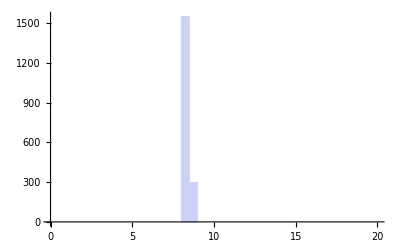

```mathematica
Histogram[tJSel[[All,3]],{0,20,.5}]
```

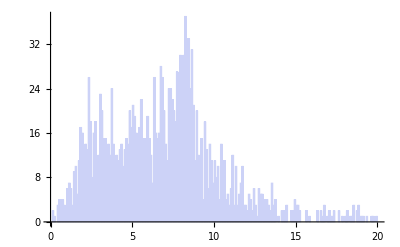

```mathematica
Histogram[convJbound[[All,3]],{0,20,.1}]
```

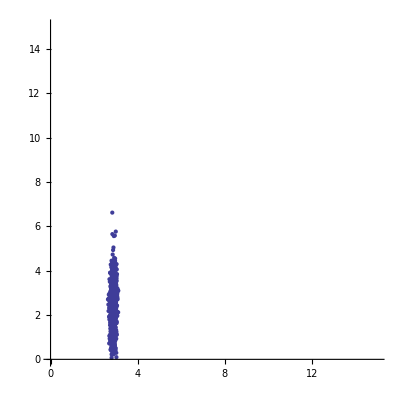

```mathematica
ListPlot[Transpose[{tJSel[[All,2]],convJbound[[All,2]]}],PlotRange->{{0,15},{0,15}},AspectRatio->1]
```

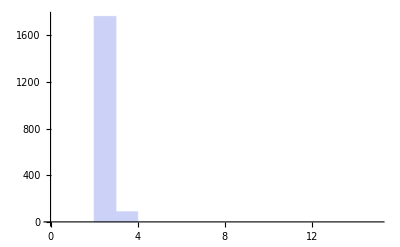

```mathematica
Histogram[tJSel[[All,2]],{0,15,1}]
```

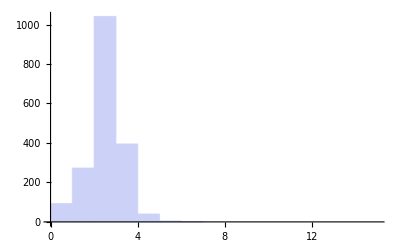

```mathematica
Histogram[convJbound[[All,2]],{0,15,1}]
```

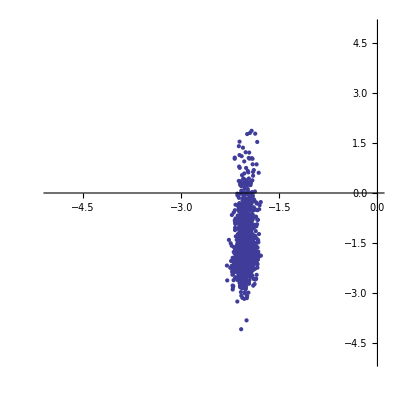

```mathematica
ListPlot[Transpose[{tJSel[[All,1]],convJbound[[All,1]]}],PlotRange->{{-5,0},{-5,5}},AspectRatio->1]
```

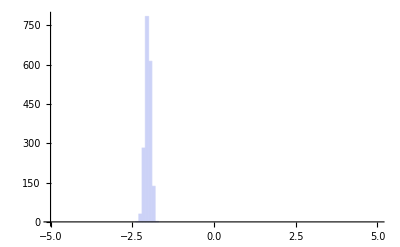

```mathematica
Histogram[tJSel[[All,1]],{-5,5,.1}]
```

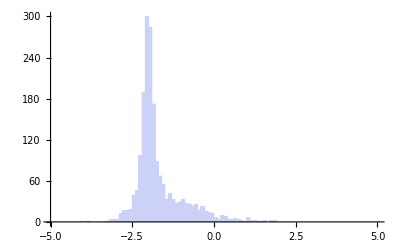

```mathematica
Histogram[convJbound[[All,1]],{-5,5,.1}]
```

Check by converting (x,v) unconvolved back to (Jr, L, Lz)

```mathematica
fnameCleanPosIn="posi.clean.dat"
fnameCleanVelIn="veli.clean.dat"
```

posi.clean.dat

veli.clean.dat

```mathematica
pStream=OpenWrite[fnameCleanPosIn,BinaryFormat->False]
vStream=OpenWrite[fnameCleanVelIn,BinaryFormat->False]
```

OutputStream[posi.clean.dat,201]

OutputStream[veli.clean.dat,202]

```mathematica
Write[pStream,Length[tpSel]];
Export[pStream,tpSel,"Data"];
Export[vStream,tvSel,"Data"];
```

```mathematica
Close[pStream]
Close[vStream]
```

posi.clean.dat

veli.clean.dat

## Run cartToAA

```mathematica
Dimensions[convJi=ReadList["newJi.test.dat",{Number,Number,Number}]]
```

{11584,3}

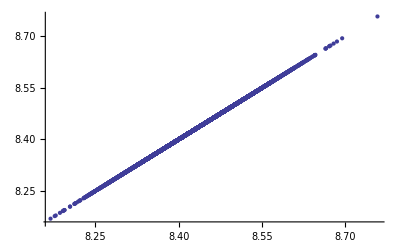

```mathematica
ListPlot[Transpose[{Pick[trueActions[[All,3]],allSels],convJi[[All,3]]}]]
```

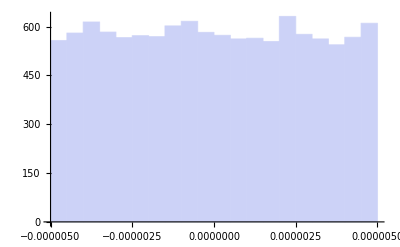

```mathematica
Histogram[Pick[trueActions[[All,3]],allSels]-convJi[[All,3]]]
```

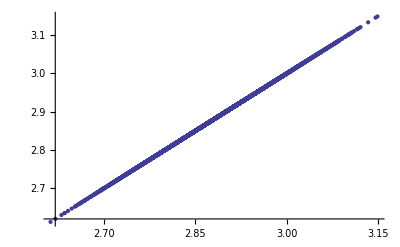

```mathematica
ListPlot[Transpose[{Pick[trueActions[[All,2]],allSels],convJi[[All,2]]}]]
```

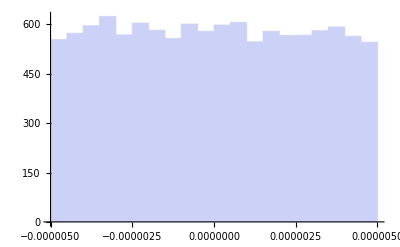

```mathematica
Histogram[Pick[trueActions[[All,2]],allSels]-convJi[[All,2]]]
```

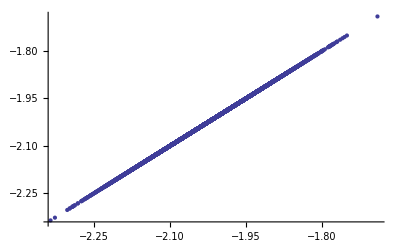

```mathematica
ListPlot[Transpose[{Pick[trueActions[[All,1]],allSels],convJi[[All,1]]}]]
```

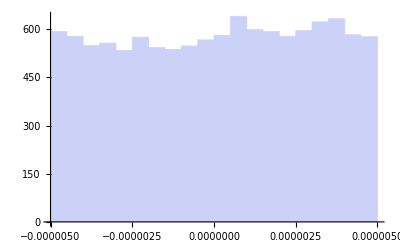

```mathematica
Histogram[Pick[trueActions[[All,1]],allSels]-convJi[[All,1]]]
```